# Задача 3

```mathematica
f[x_]=(-45(6+2)Cos[x]+x^3+23)/(6-x^2)
xt = Table[10+4+i*0.3, {i, 0, 10}]
yt = f[xt]//N
```

(23+x^3-360 Cos[x])/(6-x^2)

{14.,14.3,14.6,14.9,15.2,15.5,15.8,16.1,16.4,16.7,17.}

{-14.3041,-15.1422,-15.9098,-16.5719,-17.1052,-17.4989,-17.7548,-17.8862,-17.9157,-17.8731,-17.7917}

```mathematica
a = 14.;
b = 17.;
h = 0.3;
n = (b-a)/h;
```

```mathematica
ITochno =∫_14^17 f[x]ⅆx //N
```

-50.9355+0. ⅈ

## Леви правоъгълници

```mathematica
ILevi = h * ∑_(i=0)^(n - 1) f[a + i * h]
```

-50.3886

## Оценка на грешката

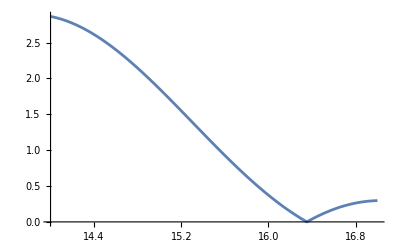

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

## Намиране на M1

```mathematica
M1 = Abs[f'[a]]//N
```

2.86371

```mathematica
RLevi =(b-a)^2/(2n)*M1
```

1.28867

## Истинска грешка

```mathematica
Print["Мрежата е със стъпка h = ", h // N, " брой подинтервали n = ", n]
Print["Приближената стойност по метода на левите правоъгълници е ", ILevi // N]
Print["Точнатата стойност е ", ITochno]
Print["Теоретичната грешка по метода на левите праовъгълници е ", RLevi // N]
Print["Истинската грешка е ", Abs[ILevi - ITochno]]
```

Мрежата е със стъпка h = 0.3 брой подинтервали n = 10.

Приближената стойност по метода на левите правоъгълници е -50.3886

Точнатата стойност е -50.9355+0. ⅈ

Теоретичната грешка по метода на левите праовъгълници е 1.28867

Истинската грешка е 0.546887

```mathematica
eps = 10^-5;
Clear[n]
```

## Леви правоъгълници с точност 0.000001

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

-Graphics-

```mathematica
M1=Abs[f'[a]]//N
```

2.86371

```mathematica
eps = 10^-6;
Clear[n]
```

```mathematica
Reduce[(b-a)^2/(2n)*M1≤eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.28867×10^7